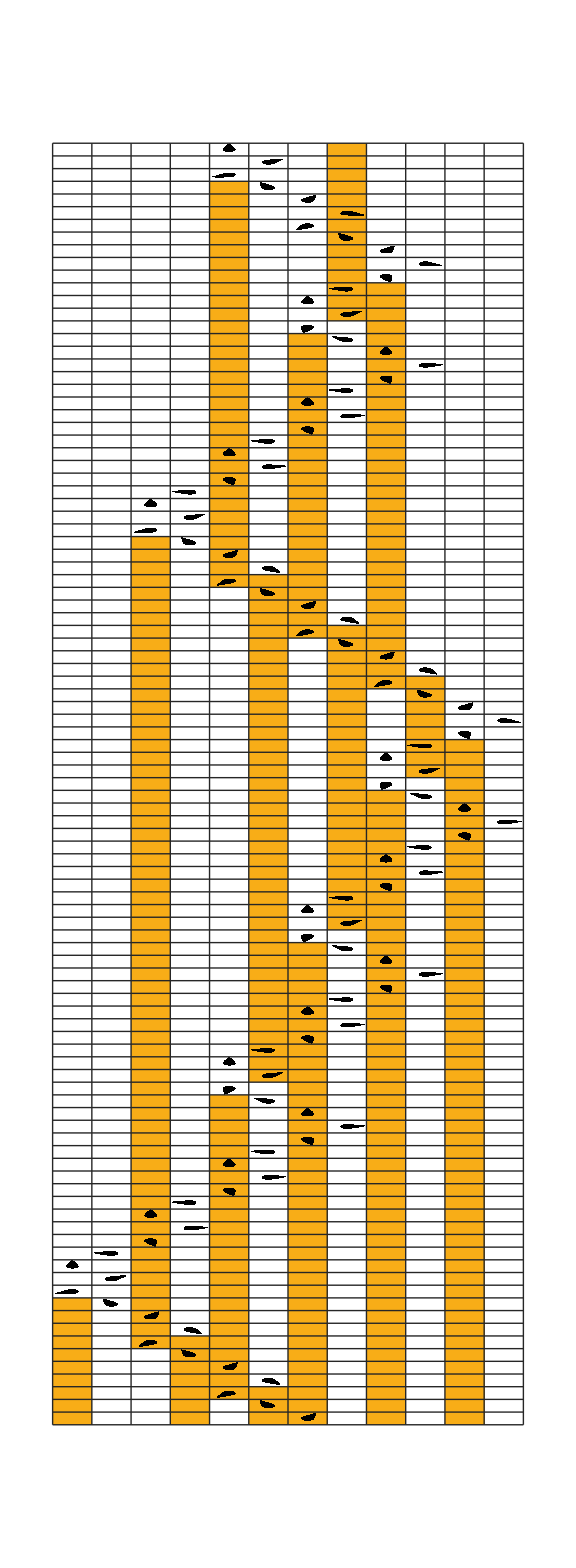

```mathematica
TMConvertRuleTo2Colors[rule_]:=Module[{numcolors=Max[rule[[All,1,2]]]+1,numstates=Max[rule[[All,1,1]]],r={},m,x,u,v,w},If[numcolors≤2,rule,m=Ceiling[Log[2,numcolors]];w=MapIndexed[#1->First[#2]&,Flatten[NestList[(r={r,x=Flatten[Table[{#,k}->Switch[#⟦3,1⟧,2,{{#⟦1⟧,Append[#⟦2⟧,k],Rest[#⟦3⟧]},k,1},3,u=FromDigits[Append[#⟦2⟧,k],2];u=If[u<numcolors,{#⟦1⟧,u}/.rule,{0,k,1}];v=IntegerDigits[u⟦2⟧,2,m];{{u⟦1⟧,Reverse@Most@v,Flatten[{Rest[#⟦3⟧],u⟦3⟧+6,Table[u⟦3⟧,{m-1}],Table[2,{m-1}],3,Table[4,{m-2}]}]},Last[v],-1},4,{{#⟦1⟧,Rest[#⟦2⟧],Rest[#⟦3⟧]},First[#⟦2⟧],-1},5,{{#⟦1⟧,{},Rest[#⟦3⟧]},First[#⟦2⟧],-1},7,{{#⟦1⟧,{},Rest[#⟦3⟧]},First[#⟦2⟧],1},_,{{#⟦1⟧,{},Rest[#⟦3⟧]},k,#⟦3,1⟧}],{k,0,1}]&/@#]};Union[Select[x[[All,-1,1]],First[#]≠0&]])&,Table[{i,{},Flatten[{Table[2,{m-1}],3,Table[4,{m-2}]}]},{i,numstates}],3m-2],1]];Flatten[r]/.w/.({a_,b_}->x_/;!MatchQ[x,{_Integer,_Integer,_Integer}])->({a,b}->{a,b,0})]];

RulePlot[TuringMachine[TMConvertRuleTo2Colors[{{1,0}->{2,2,1},{1,1}->{1,2,1},{1,2}->{1,2,-1},{2,0}->{1,2,-1},{2,1}->{2,1,1},{2,2}->{2,1,1}}]],{{1,-2},{{1},0}},100,]
```